## Adatok kinyerése

-Graphics-

az adatpontok koordinátáinak kinyerése az ábráról (Coordinates Tool):

```mathematica
koordFord={{1204.7743467933492,1170.5376088677758},{1107.8384798099762,1095.0031670625501},{1009.6437054631829,1106.333333333334},{911.4489311163895,990.5138558986546},{813.2541567695962,797.9010292953291},{715.0593824228029,836.9271575613624},{616.8646080760095,801.6777513855905},{518.6698337292162,679.5637371338087},{419.21615201900244,571.2977038796519},{321.021377672209,468.0673000791767}};
```

```mathematica
koord=Reverse[koordFord];(*sorrend megforditasa, mert az elsonek kijelolt pont az utolso a listaban*)
```

```mathematica
origoKoord=koord-Table[koord[[1]],Length[koord]];(*origo koordinatainak kivonasa*)
```

átskálázás:

```mathematica
tengelyek={{1793.8901335988714,468.0673000791767},{321.021377672209,1230.9719525350592}};(*(15,0) es (0,100) pontok koordinatai*)
```

```mathematica
x15=tengelyek[[1]]-koord[[1]];(*origoval eltolt (15,0) pont*)
```

```mathematica
y100=tengelyek[[2]]-koord[[1]];(*origoval eltolt (0,100) pont*)
```

```mathematica
normKoord=Table[
{origoKoord[[i,1]]/x15[[1]]*15,origoKoord[[i,2]]/y100[[2]]*2},
{i,1,Length[origoKoord]}
];(*atskalazas: x tengely 0-15 koze illetve y tengely 0-2 koze -- a 10-hatvanyok kitevoi*)
```

exponenciális y koordináták:

```mathematica
normKoordExp=Table[
{normKoord[[i,1]],10^normKoord[[i,2]]},
{i,1,Length[normKoord]}
];(*exponencialis y-koord*)
```

### Ábrák

ábrázolás:

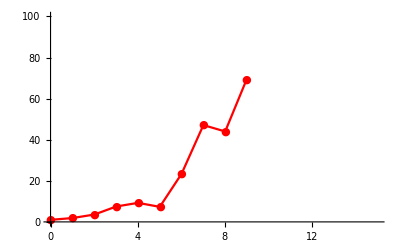

```mathematica
ListLinePlot[
normKoordExp,
PlotRange->{{0,15},{0,100}},
PlotMarkers->"●",
PlotStyle->Red
]
```

ábrázolás logaritmikus skálán (mint az eredeti):

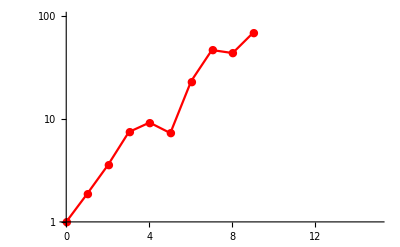

```mathematica
ListLogPlot[
normKoordExp,
PlotRange->{{0,15},{1,100}},
Joined->True,
AxesOrigin->{0,1},
PlotMarkers->"●",
PlotStyle->Red
]
```